# Project report

## Fast GC temperature program

D Malan

Department of Chemistry
University of Pretoria

18 February 2020

## Introduction

The best temperature program would be one that is controlled all the way.

Experience have shown that the temperature program must start as soon as possible. Every moment that is spent at constant temperature reduces the sharpness of the GC peaks.

## Experimental

A simulated SFC×GC chromatogram was recorded. It contained 18 GC runs. The temperature program was determined by tinkering with settings during a previous run.

2020_02_18-134737.dat

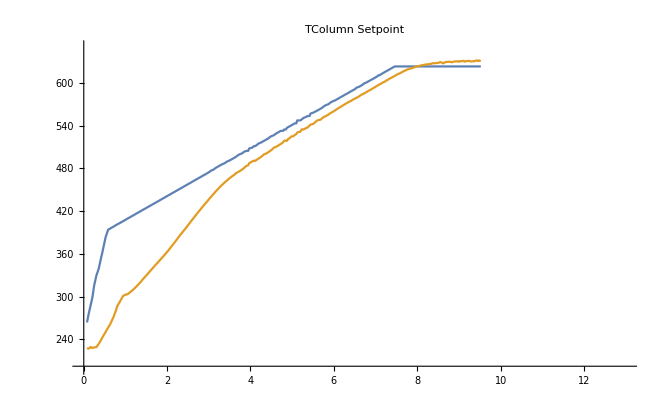

## Calculations

## Results

The coaxial heater has no control over the temperature at the low end. During the first half second or so the temperature is constant, at the trapping temperature, probably because there is some residual liquid carbon dioxide left in the space between the column and the wall of the coaxial heater. There is also some residual carbon dioxide blowing out of the length of tube between the cryo stop valve and the metering valve, but opening the metering valve more did not seem to shorten this cold period.

After this constant period there is a period of rapid temperature rise, but to about 25 °C. I attribute this rise to the coaxial heater absorbing heat from the environment.

Then, at around 1 s, there is a short stationary period, where the temperature does not seem to change. I have no ready explanation for this. It might be linked to the melting of water ice on the outside of the column.

After this time the resistive heating becomes effective and the temperature rises under PID control.

## Discussion

The temperature program above has been chosen because it keeps the stationary point at around 1s as short as possible. The temperature increase from 300 K to 450 K is ballistic: the coaxial heater gives its maximum  power, and the temperature rises at a rate of about 4500 K/min. Above 450 K the temperature is under PID control.

The longitudinal temperature gradients that might exist remain unexamined.

The 18 consecutive temperature ramps obtained are very similar and should yield good chromatograms. The first one differs slightly from the rest.

Although the temperature program obtained good enough for the chromatographic work, it is fundamentally unsatisfactory: for a great deal of the chromatogram the set point bears no resemblance to the actual temperature obtained.

## Conclusion

A temperature program was devised that starts as soon as possible and minimizes periods with constant temperature.

In its current guise the SFC×GC instrument is not suitable for the analysis of volatile compounds.

## Recommendations

Design an integrated stop/control valve for cryogen flow.

Use a high-speed camera to time the melting and evaporation of water ice, and synchronize it to the temperature measurement.

Use a high-speed thermal camera to estimate the longitudinal temperature gradients of the coaxial heater.

Switch to a real-time operating system with deterministic timing.

Discuss the best controller for this purpose with an engineer versed in control systems theory.